```mathematica
(*Tripple Dot*)
```

```mathematica
(*Spin Matrices*)
σ0=({{1, 0}, {0, 1}});
σx=({{0, 1}, {1, 0}});
σy=({{0, ⅈ}, {-ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*Majorana operators*)
γx1d=KroneckerProduct[σx,σ0,σ0,σ0,σ0,σ0];
γx1u=KroneckerProduct[σz,σx,σ0,σ0,σ0,σ0];
γx2d=KroneckerProduct[σz,σz,σx,σ0,σ0,σ0];
γx2u=KroneckerProduct[σz,σz,σz,σx,σ0,σ0];
γx3d=KroneckerProduct[σz,σz,σz,σz,σx,σ0];
γx3u=KroneckerProduct[σz,σz,σz,σz,σz,σx];

γy1d=KroneckerProduct[σy,σ0,σ0,σ0,σ0,σ0];
γy1u=KroneckerProduct[σz,σy,σ0,σ0,σ0,σ0];
γy2d=KroneckerProduct[σz,σz,σy,σ0,σ0,σ0];
γy2u=KroneckerProduct[σz,σz,σz,σy,σ0,σ0];
γy3d=KroneckerProduct[σz,σz,σz,σz,σy,σ0];
γy3u=KroneckerProduct[σz,σz,σz,σz,σz,σy];

γx={γx1u,γx1d,γx2u,γx2d,γx3u,γx3d};
γy={γy1u,γy1d,γy2u,γy2d,γy3u,γy3d};

(*Dirac operators*)
dd=Table[1/2(γx[[i]]+ⅈ γy[[i]]),{i,1,6}];
d=Table[1/2(γx[[i]]-ⅈ γy[[i]]),{i,1,6}];
```

```mathematica
(*Parameters*)
α=0.05;  (*Spin Orbit Coupling*)
Δ1=0.2;  (*Induced Superconducing Gap on Dot 1*)
Δ2=0.2;  (*Induced Superconducing Gap on Dot 2*)
Δ3=0.2;  (*Induced Superconducing Gap on Dot 3*)
B=0.2;  (*Magnetic Field*)
t12=-0.3;  (*Hopping* between dots one and two*)
t23=-0.3;  (*Hopping* between dots two and three*)
U=0.01;  (*Electron-Electron interaction*)
ev=0.05;  (*Voltage*)
ϵ1=0.2;  (*Potential for Dot One*)
ϵ2=0.2;  (*Potential for Dot Two*)
ϵ3=0.2;  (*Potential for Dot Three*)
ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
t={t12,t12,t23,t23};
Δ={Δ1,Δ1,Δ2,Δ2,Δ3,Δ3};
Eϵ=Table[{},{n,1,2^6}];
```

```mathematica
Eϵ=Table[{},{n,1,2^6}];
nϵ=Table[{},{n,1,2^6}];
Ψl=Table[{},{n,1,2^6}];
gxl={};
gyl={};
For[ϵt=-0.5,ϵt≤0.5,ϵt+=0.02,
ϵ1=ϵt;
ϵ2=ϵt;
ϵ3=ϵt;
ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
(*Hamiltonian*)
Hd3=Sum[ϵ[[i]](dd[[i]].d[[i]]-d[[i]].dd[[i]]),{i,1,6}]+ Sum[t[[i]](dd[[i+2]].d[[i]]+dd[[i]].d[[i+2]]),{i,1,4}]+B Sum[dd[[i+1]].d[[i]]+dd[[i]].d[[i+1]],{i,1,5,2}]+α Sum[dd[[i]].d[[i+3]]+dd[[i+3]].d[[i]]-dd[[i+1]].d[[i+2]]-dd[[i+2]].d[[i+1]],{i,1,4,2}]+ Sum[Δ[[i]](dd[[i+1]].dd[[i]]+d[[i]].d[[i+1]]),{i,1,5,2}]+U Sum[dd[[i]].d[[i]].dd[[i+1]].d[[i+1]],{i,1,5,2}];{e,Ψ}=Transpose[Sort[Transpose[Eigensystem[Hd3]]]];
n0=Table[Table[{i,Abs[Conjugate[Ψ[[n]]].dd[[i]].d[[i]].Ψ[[n]]]^2},{i,1,6}],{n,1,Length[Ψ]}];
gx=Table[{i,Abs[Conjugate[Ψ[[2]]].γx[[i]].Ψ[[1]]]^2},{i,1,6}];
gy=Table[{i,Abs[Conjugate[Ψ[[2]]].γy[[i]].Ψ[[1]]]^2},{i,1,6}];

gxl=Join[gxl,{gx}];
gyl=Join[gyl,{gy}];
For[n=1,n≤2^6,n++,
Eϵ[[n]]=Join[Eϵ[[n]],{{ϵt,e[[n]]-e[[1]]}}];
nϵ[[n]]=Join[nϵ[[n]],{n0[[n]]}];
Ψl[[n]]=Join[Ψl[[n]],{Ψ[[n]]}];
];
];
```

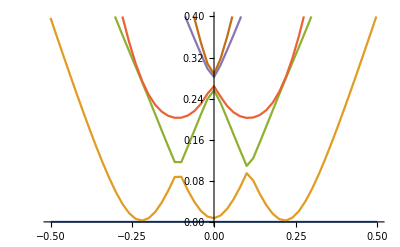

```mathematica
ListPlot[Eϵ,PlotRange->{0.0,2Δ1},Joined->True]
```

```mathematica
Manipulate[{ListPlot[{gxl[[bi]],gyl[[bi]]}],Eϵ[[2,bi]]},{bi,1,Length[gxl],1}]
```

```mathematica
Manipulate[{ListPlot[{nϵ[[1,bi]],nϵ[[2,bi]]},Ticks->{{{1,"1u"}, {2, "1d"}, {3,"2u"}, {4,"2d"},{ 5,"3u"}, {6,"3d"}}, Automatic}],Eϵ[[2,bi]]},{bi,1,Length[Eϵ[[1]]],1}]
```

```mathematica
ϵ1=0.5;
ϵ2=0.5;
ϵ3=0.5;
ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
B=0.22;
Hd3=Sum[ϵ[[i]](dd[[i]].d[[i]]-d[[i]].dd[[i]]),{i,1,6}]+ Sum[t[[i]](dd[[i+2]].d[[i]]+dd[[i]].d[[i+2]]),{i,1,4}]+B Sum[dd[[i+1]].d[[i]]+dd[[i]].d[[i+1]],{i,1,5,2}]+α Sum[dd[[i]].d[[i+3]]+dd[[i+3]].d[[i]]-dd[[i+1]].d[[i+2]]-dd[[i+2]].d[[i+1]],{i,1,4,2}]+ Sum[Δ[[i]](dd[[i+1]].dd[[i]]+d[[i]].d[[i+1]]),{i,1,5,2}]+U Sum[dd[[i]].d[[i]].dd[[i+1]].d[[i+1]],{i,1,5,2}];{e,Ψ}=Transpose[Sort[Transpose[Eigensystem[Hd3]]]];
n0=Table[Table[{i,Abs[Conjugate[Ψ[[n]]].dd[[i]].d[[i]].Ψ[[n]]]^2},{i,1,6}],{n,1,Length[Ψ]}];
gx=Table[{i,Abs[Conjugate[Ψ[[2]]].γx[[i]].Ψ[[1]]]^2},{i,1,6}];
gy=Table[{i,Abs[Conjugate[Ψ[[2]]].γy[[i]].Ψ[[1]]]^2},{i,1,6}];
e[[2]]-e[[1]]
```

0.386663

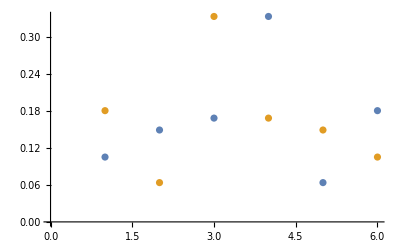

```mathematica
ListPlot[{gx,gy}]
```

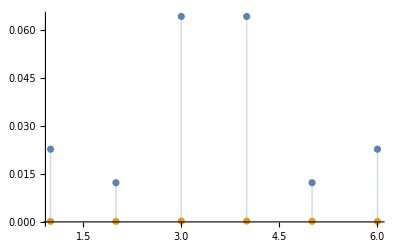

```mathematica
ListPlot[{n0[[2]],n0[[1]]},Filling->Axis,PlotRange->All]
```

```mathematica
Ptotal=Table[Conjugate[Ψ[[n]]].γx[[1]].γy[[1]].γx[[2]].γy[[2]].γx[[3]].γy[[3]].γx[[4]].γy[[4]].γx[[5]].γy[[5]].γx[[6]].γy[[6]].Ψ[[n]],{n,1,Length[Ψ]}];
```

```mathematica
ntotal=Table[{n,Sum[Abs[n0[[n,i,2]]]^2,{i,1,6}]},{n,1,Length[n0]}];
```

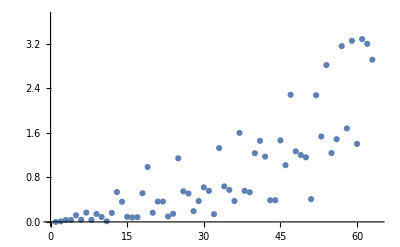

```mathematica
ListPlot[ntotal]
```

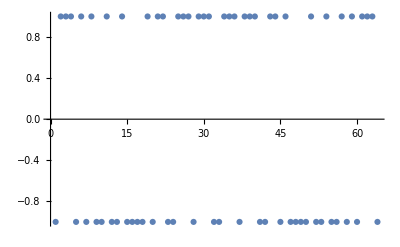

```mathematica
ListPlot[Ptotal]
```